```mathematica
α = 1/137
f[x_,s_] := ((α^2)/(4*(s^2)))*((3+Cos[x])/(1-Cos[x]))^2
```

1/137

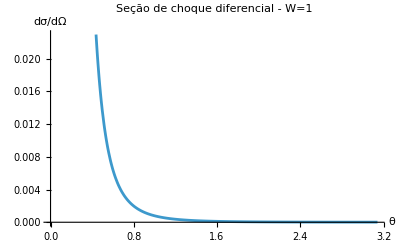

```mathematica
Plot[f[x,1],{x,0,Pi}, AxesLabel->{"θ","dσ/dΩ"},PlotLabel->"Seção de choque diferencial - W=1"]
```

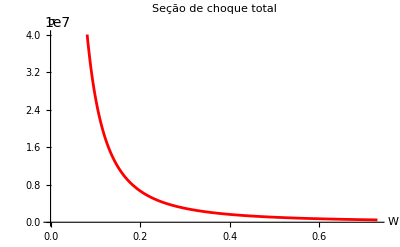

```mathematica
y[s_]:=NIntegrate[f[x,s]*Sin[x]*2*Pi,{x,0.0001,Pi}]
Plot[y[x],{x,0,100*α},AxesLabel->{"W","σ"}, PlotLabel->"Seção de choque total", PlotStyle->Red]
```